## #32

```mathematica
f[t_]=(1-UnitStep[t-2]);
```

```mathematica
Solve[LaplaceTransform[x''[t]+5x'[t]+5x[t]==f[t],t,s]/.{x[0]->0,x'[0]->0},LaplaceTransform[x[t],t,s]]
```

{{LaplaceTransform[x[t],t,s]→(ⅇ^(-2 s) (-1+ⅇ^(2 s)))/(s (5+5 s+s^2))}}

```mathematica
InverseLaplaceTransform[(ⅇ^(-2 s) (-1+ⅇ^(2 s)))/(s (5+5 s+s^2)), s, t]
```

1/10 (ⅇ^(-1/2 (5+√5) t) (-1+√5-(1+√5) ⅇ^(√5 t)+2 ⅇ^(1/2 (5+√5) t))+ⅇ^(-1/2 (5+√5) (-2+t)) (1-√5+(1+√5) ⅇ^(√5 (-2+t))-2 ⅇ^(1/2 (5+√5) (-2+t))) HeavisideTheta[-2+t])

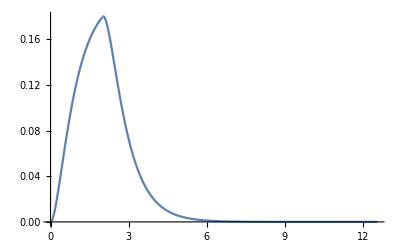

```mathematica
Plot[%,{t,0,4Pi},PlotRange->All]
```

## #41

```mathematica
f[t_]=4(2UnitStep[(t-Pi)(t-2Pi)(t-3Pi)(t-4Pi)(t-5Pi)(t-6Pi)]-1)
```

4 (-1+2 UnitStep[(-6 π+t) (-5 π+t) (-4 π+t) (-3 π+t) (-2 π+t) (-π+t)])

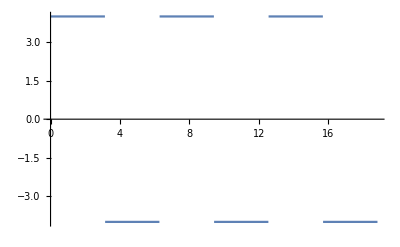

```mathematica
Plot[f[t],{t,0,6Pi}]
```

```mathematica
Solve[LaplaceTransform[x''[t]+4x[t]==f[t],t,s]/.{x[0]->0,x'[0]->0},LaplaceTransform[x[t],t,s]]
```

{{LaplaceTransform[x[t],t,s]→-(4 ⅇ^(-3 π s) (2+ⅇ^(3 π s)-4 Cosh[π s]+4 Cosh[2 π s]-4 Cosh[3 π s]))/(s (4+s^2))}}

```mathematica
InverseLaplaceTransform[-(4 ⅇ^(-3 π s) (2+ⅇ^(3 π s)-4 Cosh[π s]+4 Cosh[2 π s]-4 Cosh[3 π s]))/(s (4+s^2)),s,t]
```

2 (1+2 HeavisideTheta[-6 π+t]-2 HeavisideTheta[-5 π+t]+2 HeavisideTheta[-4 π+t]-2 HeavisideTheta[-3 π+t]+2 HeavisideTheta[-2 π+t]-2 HeavisideTheta[-π+t]) Sin[t]^2

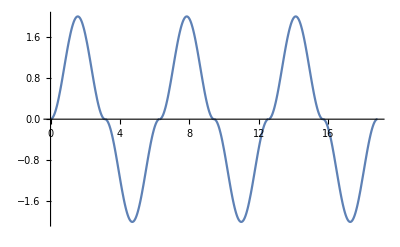

```mathematica
Plot[%,{t,0,6Pi}]
```